```mathematica
temperature=500;
dimension=5;
Nspace=5;
EstthermoForceCurFluc=Table[
temp=Table[
CurFluc=Flatten[Import[NotebookDirectory[]<>"../data/FiveBeadsConvergence/CurFluc_"<>ToString[dimension]<>"D_"<>ToString[temperature]<>"_"<>ToString[datalength]<>"_"<>ToString[count] <>"_"<>ToString[Nspace] <>".mat"]];

dt=0.001*Nspace;
L=Length[CurFluc];
(*NChop=1200/datalength;
NChop=If[datalength==12,20,NChop];
Tobs=20/NChop;*)
Tobs=1;
thermoΔJd=Table[CurFluc[[i]] - CurFluc[[i-Tobs/dt]],{i,( 1/NChop+Tobs)/dt, L-1,1/(NChop*dt)}];
Subscript[μ, 1]=Chop[Mean[thermoΔJd]/Tobs];
Subscript[var, 1] =Tobs Variance[thermoΔJd/Tobs]; 
Σ=2 Subscript[μ, 1]^2/Subscript[var, 1]
(*Print["Temperature"<>ToString[temperature] <>" Length"<>ToString[datalength] <>" Dissipation "<>ToString[Σ] <>"."];*)
(*Σ*)
,{count,1,10}];
{datalength,temp},{datalength,{12,120,1200,12000}}];
```

```mathematica
<<ErrorBarLogPlots`
DissipationAna=Import[NotebookDirectory[]<>"../data/Dissipation_Temperature.mat"][[1]];
```

```mathematica
EstthermoForceCurFlucPlot=Table[
{EstthermoForceCurFluc[[i]][[1]],Mean[EstthermoForceCurFluc[[i]][[2]]]/DissipationAna[[temperature/10-1,1]],StandardDeviation[EstthermoForceCurFluc[[i]][[2]]]/DissipationAna[[temperature/10-1,1]]}
,{i,1,4}];
```

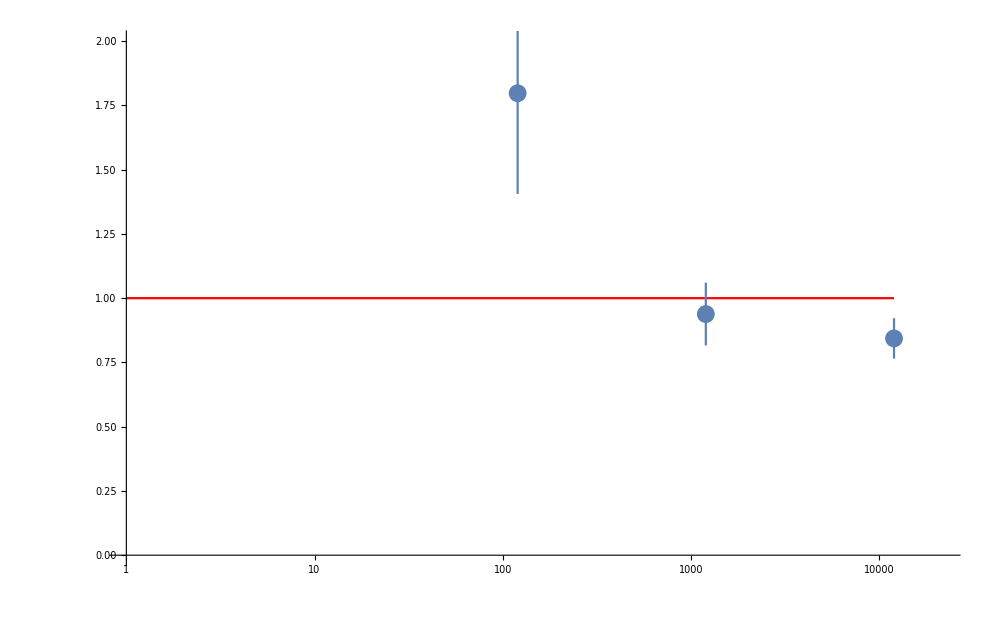

```mathematica
Show[
LogLinearPlot[1,{x,1,12000},PlotStyle->Red],
ErrorListLogLinearPlot[EstthermoForceCurFlucPlot],
PlotRange->{{0,10},{0,2}},
ImageSize->1000
]
```